```mathematica
Clear[hbar, e0, m0, ηm];
hbar=6.58211899*10^(-16);  (* h/2π  in eV s *)
m0=9.10938215*10^(-31); 
e0=1.602176487*10^(-19);
ηm=hbar^2*e0*10^(20)/m0;  (* hbar^2/m0 in eV A^2 *)
μB=5.7883818066 * 10^(-2);    (* in meV/T *)
meVpK=8.6173325*10^(-2);   (* Kelvin into meV *)
(* **************************************** *)
```

```mathematica
Clear[ts, tsw, as, ms, Nx, Ny, Nxn, α, αw, Δ];
as=10.0; (* unit cell in A *)
ms=0.04;
ts=1000*ηm/(2*as^2*ms) ;(* hopping in meV *)
α=203.0/as ;(* Rashba coupling in meV *)
Δ=0.09; (* induced gap in meV *)
Nx=250;
Nx3=250;
NxM=40;
Nxn=0;
Ny=1;
μ=0.0;

tϕ1=ts;
tϕ2=ts*0;
tϕ3=ts;



gx=2. Δ;
gy=2. Δ;

(*TriangleMagnets_ExternalField: DDD has gate controlled braiding*)
(*Gate Strengths;  Multiply by zero to turn of gate*)
u1 = 1000*0;
u2 = 1000*0;
u3 = 1000*0;

(*
(*For two middle*)
gx=0.0104;
gy=0.0104;
*)
```

```mathematica
(*Nmid = 200;
MagXTop = Table[1-HeavisideTheta[i+1/2-Nx]-HeavisideTheta[i+1/2-Nx-Nmid],{i,0,2Nx+Nmid}];
MagYTop = Table[HeavisideTheta[i+1/2-Nx]-HeavisideTheta[i+1/2-Nx-Nmid],{i,0,2Nx+Nmid}];

MagXLeg =  Table[0,{i,0,2Nx+NxM}];
MagYLeg =  Table[1,{i,0,2Nx+NxM}];*)

Nmid = 2000;
MagXTop = Table[ⅇ^(-(i-Nx/2)^2/Nx^2)+12 ⅇ^(-(i-Nx-NxM/2)^2/NxM^2)-ⅇ^(-(i-Nx-NxM-Nx/2)^2/Nx^2),{i,0,2Nx+NxM}];
MagYTop = Table[-12 ⅇ^(-(i-Nx-NxM/2)^2/NxM^2),{i,0,2Nx+NxM}];

MagXLeg =  Table[12 ⅇ^(-(i^2/NxM^2)),{i,0,Nx}];
MagYLeg =  Table[-12 ⅇ^(-(i)^2/NxM^2)+ⅇ^(-(i-Nx/2)^2/Nx^2),{i,0,Nx}];
```

```mathematica
MagΔXTop=Table[gx*MagXTop[[Ceiling[ii*Length[MagXTop]/(2Nx+NxM)]]],{ii,1,2Nx+NxM}];
MagΔYTop=Table[gy*MagYTop[[Ceiling[ii*Length[MagYTop]/(2Nx+NxM)]]],{ii,1,2Nx+NxM}];
GapTop=Table[Δ,{i,1,Length[MagΔXTop]}];
MagΔXLeg=Table[gx*MagXLeg[[Ceiling[ii*Length[MagXLeg]/(Nx3)]]],{ii,1,Nx3}];
MagΔYLeg=Table[gx*MagYLeg[[Ceiling[ii*Length[MagYLeg]/(Nx3)]]],{ii,1,Nx3}];

GapLeg=Table[Δ,{i,1,Length[MagΔXLeg]}];
```

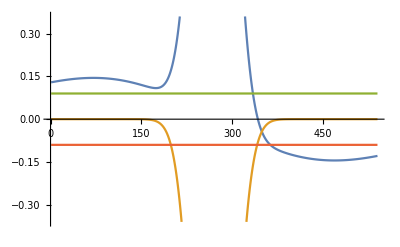

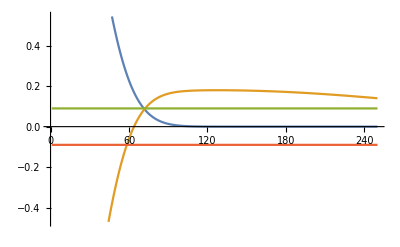

```mathematica
ListPlot[{MagΔXTop,MagΔYTop,GapTop,-GapTop},Joined->True]
ListPlot[{MagΔXLeg,MagΔYLeg,GapLeg,-GapLeg},Joined->True]
```

```mathematica
MagX1=Table[MagΔXTop[[i]],{i,1,Nx}];
MagY1=Table[MagΔYTop[[i]],{i,1,Nx}];
MagXM=Table[MagΔXTop[[i]],{i,Nx+1,Nx+NxM}];
MagYM=Table[MagΔYTop[[i]],{i,Nx+1,Nx+NxM}];
MagX2=Table[MagΔXTop[[i]],{i,Nx+NxM+1,2Nx+NxM}];
MagY2=Table[MagΔYTop[[i]],{i,Nx+NxM+1,2Nx+NxM}];
MagX3=MagΔXLeg;
MagY3=MagΔYLeg;
```

```mathematica
U1 = Table[0,{i,1,Nx}];
For[i=0,i≤5,i++,
U1[[Nx-i]]=u1;
];
UM = Table[0,{i,1,NxM}];
U2=Table[0,{i,1,Nx}];
For[i=1,i≤7,i++,
U2[[i]]=u2;
];
U3=Table[0,{i,1,Nx3}];
For[i=1,i≤4,i++,
U3[[i]]=u3;
];
```

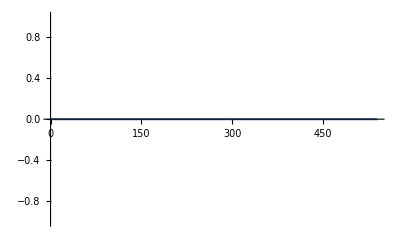

```mathematica
ListPlot[Join[U1,UM,U2],Joined->True]
```

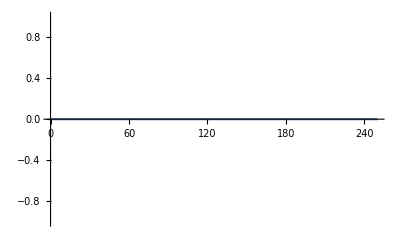

```mathematica
ListPlot[U3,Joined->True]
```

```mathematica
ϵ0=2 ts Cos[Pi/(Nx+1.0)];
(*ϵ0=2 ts Cos[Pi/(Nx+NxM/2+Nx3+1.0)];*)
(*ϵ0=2 ts Cos[Pi/(2*Nx+NxM+1.0)];*)
Clear[H]
H[θM_]:=Block[{Hsp},


(*First Chain*)
(*Spin up electron - chem, onsite energy, energy from y field and also gates (which is like chem). Ofd diagonal is hopping *)
H1σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+U1,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
(*Spin up electron*)
H1σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+U1,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
(*Coupling betweem spin up and down, hence why it is off diagonal. Magnetic field couples them via SOC*)
H1σ12τ11=SparseArray[{Band[{1,1}]->MagX1+ⅈ MagY1,Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H1σ21τ11=SparseArray[{Band[{1,1}]->MagX1-ⅈ MagY1,Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

(*Coupling betweem spin up and down particle and hole. This is what allows superpostion of particle hole states to make MF? This uses the superconductivty*)
H1σ12τ12=SparseArray[{Band[{1,1}]->Δ},{Nx,Nx}];
H1σ21τ12=SparseArray[{Band[{1,1}]->-Δ},{Nx,Nx}];

(*Coupling betweem spin up and down*)
H1τ11=SparseArray[ArrayFlatten[{{H1σ11τ11,H1σ12τ11},{H1σ21τ11,H1σ22τ11}}]]; (*For all particles*)
H1τ22=-Conjugate[H1τ11];  (*Negative as for holes*)
H1τ12=SparseArray[ArrayFlatten[{{0,H1σ12τ12},{H1σ21τ12,0}}]];
H1τ21=Conjugate[Transpose[H1τ12]];


H11=SparseArray[ArrayFlatten[{{H1τ11,H1τ12},{H1τ21,H1τ22}}]];

(*Middle Chain*)
HMσ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+UM,Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+UM,Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ12τ11=SparseArray[{Band[{1,1}]->MagXM+ⅈ MagYM,Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{NxM,NxM}];
HMσ21τ11=SparseArray[{Band[{1,1}]->MagXM-ⅈ MagYM,Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{NxM,NxM}];

HMσ12τ12=SparseArray[{Band[{1,1}]->Δ },{NxM,NxM}];
HMσ21τ12=SparseArray[{Band[{1,1}]->-Δ },{NxM,NxM}];

HMτ11=SparseArray[ArrayFlatten[{{HMσ11τ11,HMσ12τ11},{HMσ21τ11,HMσ22τ11}}]];
HMτ22=-Conjugate[HMτ11];
HMτ12=SparseArray[ArrayFlatten[{{0,HMσ12τ12},{HMσ21τ12,0}}]];
HMτ21=Conjugate[Transpose[HMτ12]];

HMM=SparseArray[ArrayFlatten[{{HMτ11,HMτ12},{HMτ21,HMτ22}}]];



(*Second Chain*)
H2σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+U2,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+U2,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ12τ11=SparseArray[{Band[{1,1}]->MagX2+ⅈ MagY2,Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H2σ21τ11=SparseArray[{Band[{1,1}]->MagX2-ⅈ MagY2,Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H2σ12τ12=SparseArray[{Band[{1,1}]->Δ },{Nx,Nx}];
H2σ21τ12=SparseArray[{Band[{1,1}]->-Δ },{Nx,Nx}];

H2τ11=SparseArray[ArrayFlatten[{{H2σ11τ11,H2σ12τ11},{H2σ21τ11,H2σ22τ11}}]];
H2τ22=-Conjugate[H2τ11];
H2τ12=SparseArray[ArrayFlatten[{{0,H2σ12τ12},{H2σ21τ12,0}}]];
H2τ21=Conjugate[Transpose[H2τ12]];

H22=SparseArray[ArrayFlatten[{{H2τ11,H2τ12},{H2τ21,H2τ22}}]];

(*Third Chain*)
H3σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+U3,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx3,Nx3}];
H3σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+U3,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx3,Nx3}];
H3σ12τ11=SparseArray[{Band[{1,1}]-> MagX3+ⅈ MagY3,Band[{1,2}]->-ⅈ α/2,Band[{2,1}]->ⅈ α/2},{Nx3,Nx3}];
H3σ21τ11=SparseArray[{Band[{1,1}]->MagX3-ⅈ MagY3,Band[{1,2}]->-ⅈ α/2,Band[{2,1}]->ⅈ α/2},{Nx3,Nx3}];

H3σ12τ12=SparseArray[{Band[{1,1}]->Δ },{Nx3,Nx3}];
H3σ21τ12=SparseArray[{Band[{1,1}]->-Δ },{Nx3,Nx3}];

H3τ11=SparseArray[ArrayFlatten[{{H3σ11τ11,H3σ12τ11},{H3σ21τ11,H3σ22τ11}}]];
H3τ22=-Conjugate[H3τ11];
H3τ12=SparseArray[ArrayFlatten[{{0,H3σ12τ12},{H3σ21τ12,0}}]];
H3τ21=Conjugate[Transpose[H3τ12]];

H33=SparseArray[ArrayFlatten[{{H3τ11,H3τ12},{H3τ21,H3τ22}}]];

(*Tunnel Junction*)
H1M=SparseArray[{{Nx,1}->tϕ1,{2Nx,NxM+1}->tϕ1,{3Nx,2NxM+1}->-tϕ1,{4Nx,3NxM+1}->-tϕ1},{4Nx,4NxM}];(*tunneling for all different types of partciles? I.e. spin up/down particle/holes. This is within one chunk connecting all different particles from end of H11 chain to middle chain. Holes are negative hoping?*)
HM1=Conjugate[Transpose[H1M]];

HM2=SparseArray[{{NxM,1}->tϕ2,{2NxM,Nx+1}->tϕ2,{3NxM,2Nx+1}->-tϕ2,{4NxM,3Nx+1}->-tϕ2},{4NxM,4Nx}];
H2M=Conjugate[Transpose[HM2]];

HM3=SparseArray[{{NxM/2,1}->tϕ3,{NxM+NxM/2,Nx3+1}->tϕ3,{2NxM+NxM/2,2Nx3+1}->-tϕ3,{3NxM+NxM/2,3Nx3+1}->-tϕ3},{4NxM,4Nx3}];
H3M=Conjugate[Transpose[HM3]];

(*Full Wire*)
Hsp=SparseArray[ArrayFlatten[{{H11,H1M,0,0},{HM1,HMM,HM2,HM3},{0,H2M,H22,0},{0,H3M,0,H33}}]];
(*dimsize=Dimensions[Hsp];*)
Hsp
];
(*dimsize;*)
NxM;
nc=20;(*Number of values?*)
{e,ψ}=Transpose[Sort[Transpose[Eigensystem[H[0.],-nc]]]];
```

```mathematica
nc=20;
{e,ψ}=Transpose[Sort[Transpose[Eigensystem[H[0.],-nc]]]];
```

```mathematica
e[[nc/2+2]]
e[[nc/2-1]]
```

0.0311174

-0.0311174

```mathematica
n=11;
e[[n]]/Δ
ψA1ue=Table[{i-1,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2Nx+i]]]^2+Abs[ψ[[n,3Nx+i]]]^2},{i,1,Nx}];
ψAMue=Table[{i-1-3Nx,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,NxM+i]]]^2+Abs[ψ[[n,2NxM+i]]]^2+Abs[ψ[[n,3NxM+i]]]^2},{i,4Nx,4Nx+NxM}];
ψA2ue=Table[{i-1-3Nx-3NxM,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2Nx+i]]]^2+Abs[ψ[[n,3Nx+i]]]^2},{i,4Nx+4NxM,4Nx+4NxM+Nx}];

ψA3ue=Table[{i+1-4Nx-4NxM-4Nx,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx3+i]]]^2+Abs[ψ[[n,2Nx3+i]]]^2+Abs[ψ[[n,3Nx3+i]]]^2},{i,4Nx+4NxM+4Nx,4Nx+4NxM+4Nx+Nx3}];
ψbar=Join[ψA1ue,ψAMue,ψA2ue];
ψleg=ψA3ue;
```

0.225247

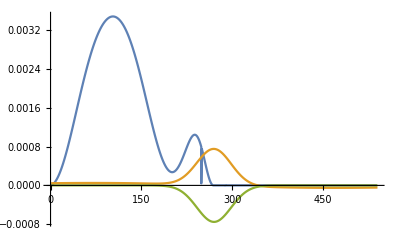

```mathematica
w=Max[Table[ψbar[[i,2]],{i,1,Length[ψbar]}]]/10;
ListPlot[{ψbar,w MagΔXTop,w MagΔYTop},Joined->True,PlotRange->All]
```

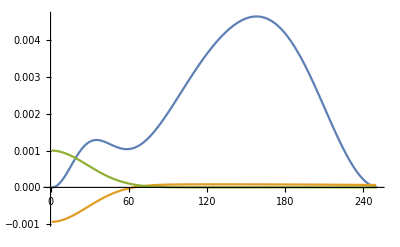

```mathematica
w=Max[Table[ψleg[[i,2]],{i,1,Length[ψleg]}]]/10;
ListPlot[{ψleg,w MagΔYLeg,w MagΔXLeg},Joined->True,PlotRange->All]
```